#### Problem 9.2.9bc

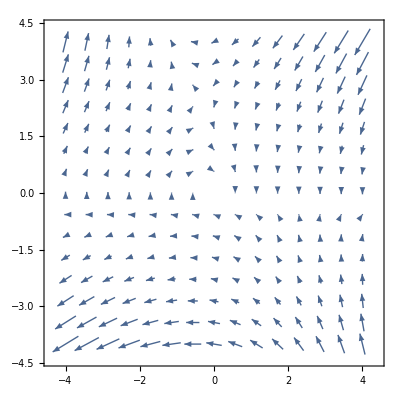

```mathematica
VectorPlot[{y*(2-x-y),-x-y-2*x*y},{x,-4,4},{y,-4,4}]
```

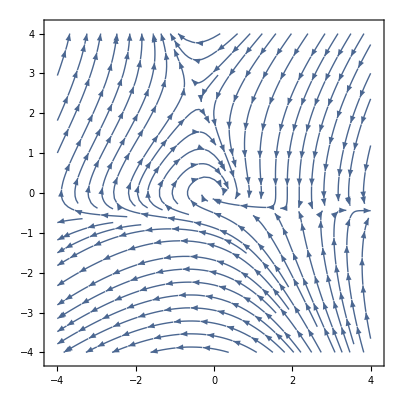

```mathematica
StreamPlot[{y*(2-x-y),-x-y-2*x*y},{x,-4,4},{y,-4,4}]
```

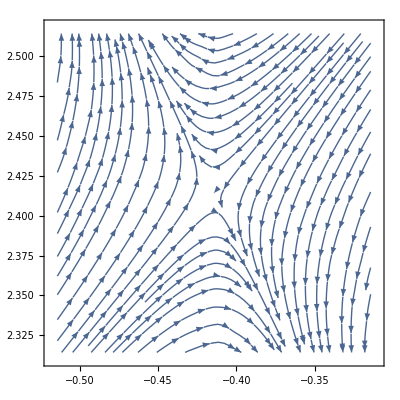

```mathematica
StreamPlot[{y*(2-x-y),-x-y-2*x*y},{x,1-(2^0.5)-.1,1-(2^0.5)+.1},{y,1+(2^0.5)-.1,1+(2^0.5)+.1}]
```

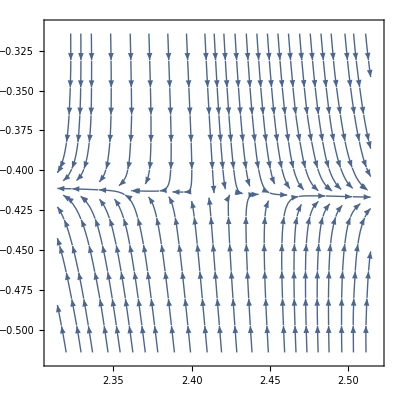

```mathematica
StreamPlot[{y*(2-x-y),-x-y-2*x*y},{x,1+(2^0.5)-.1,1+(2^0.5)+.1},{y,1-(2^0.5)-.1,1-(2^0.5)+.1}]
```

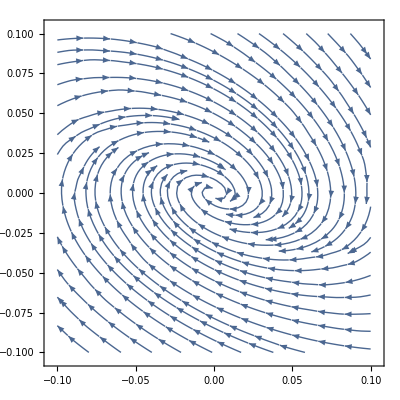

```mathematica
StreamPlot[{y*(2-x-y),-x-y-2*x*y},{x,-.1,.1},{y,-.1,.1}]
```

#### Problem 9.2.21b

```mathematica
f[x_,y_]:=-2*x*y+0.5*(y^2)+2*(x^2)*y
```

```mathematica
Plot[{f[x,y]==0,f[x,y]=1,f[x,y]=2}, {x,-10,10},{y,-10,10}]
```

Plot::nonopt: Options expected (instead of {y,-10,10}) beyond position 2 in Plot[{f[x,y]==0,f[x,y]=1,f[x,y]=2},{x,-10,10},{y,-10,10}]. An option must be a rule or a list of rules.

Plot[{f[x,y]==0,f[x,y]=1,f[x,y]=2},{x,-10,10},{y,-10,10}]

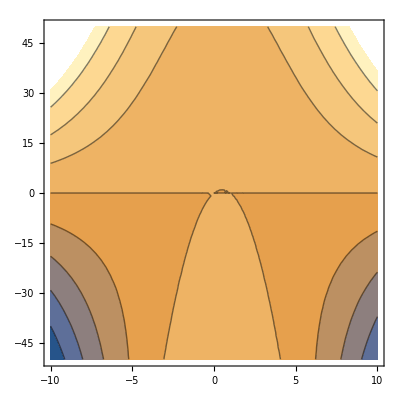

```mathematica
ContourPlot[Callout[-2*x*y+0.5*(y^2)+2*(x^2)*y, "c=-1000"], {x,-10,10},{y,-50,50}]
```

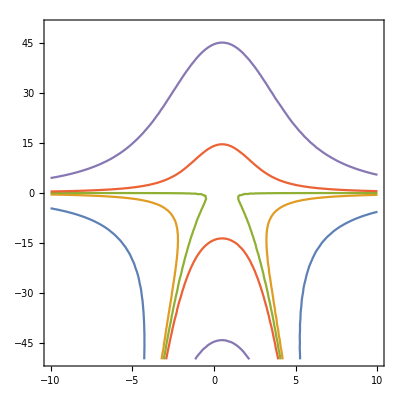

```mathematica
ContourPlot[{f[x,y]==-1000,f[x,y]==-100,f[x,y]==-1,f[x,y]==100,f[x,y]==1000},{x,-10,10},{y,-50,50}]
```

```mathematica
ContourPlot3D[f[x,y]==z, {x,-10,10},{y,-100,100}, {z,-1000,1000}]
```

-Graphics3D-

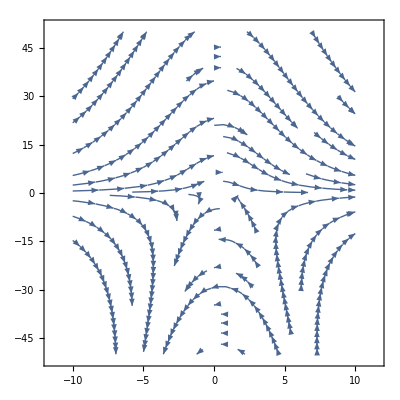

```mathematica
StreamPlot[{-x+y+x^2,y-2*x*y},{x,-10,10},{y,-50,50}]
```

#### Problem 9.3.5d

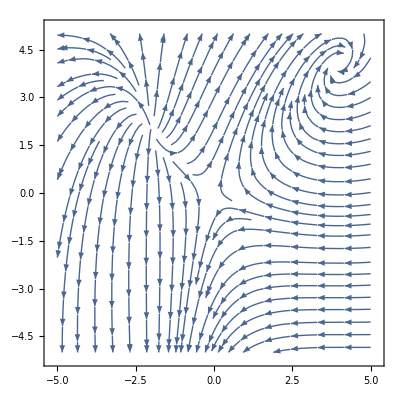

```mathematica
StreamPlot[{(2+x)*(y-x),(4-x)*(y+x)},{x,-5,5},{y,-5,5}]
```

#### Problem 9.3.6d

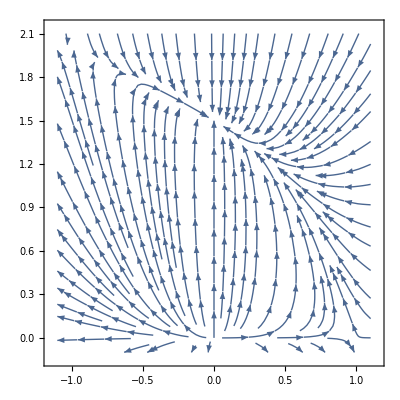

```mathematica
StreamPlot[{x-(x^2)-(x*y), (3*y)-(x*y)-2*(y^2)},{x,-1.1,1.1},{y,-0.1,2.1}]
```

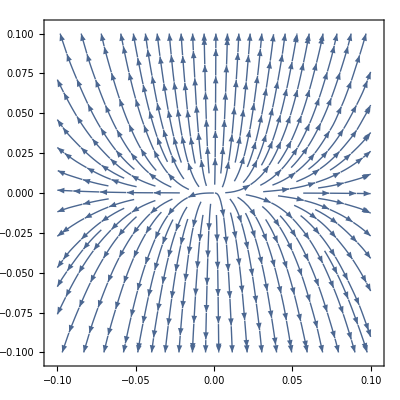

```mathematica
StreamPlot[{x-(x^2)-(x*y), (3*y)-(x*y)-2*(y^2)},{x,-0.1,0.1},{y,-0.1,0.1}]
```

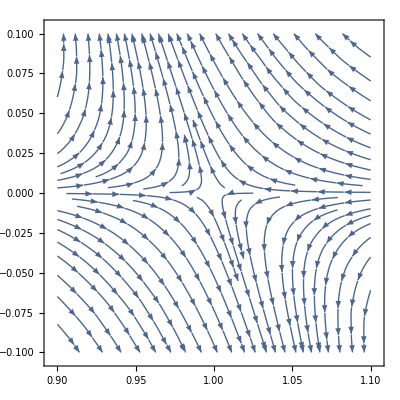

```mathematica
StreamPlot[{x-(x^2)-(x*y), (3*y)-(x*y)-2*(y^2)},{x,0.9,1.1},{y,-0.1,0.1}]
```

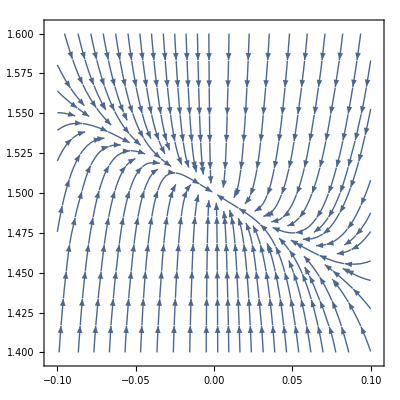

```mathematica
StreamPlot[{x-(x^2)-(x*y), (3*y)-(x*y)-2*(y^2)},{x,-.1,0.1},{y,1.4,1.6}]
```

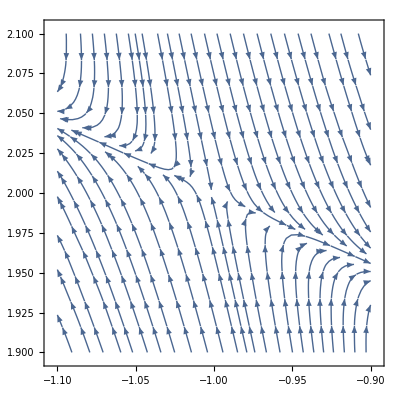

```mathematica
StreamPlot[{x-(x^2)-(x*y), (3*y)-(x*y)-2*(y^2)},{x,-1.1,-0.9},{y,1.9,2.1}]
```

#### Problem 9.3.8d

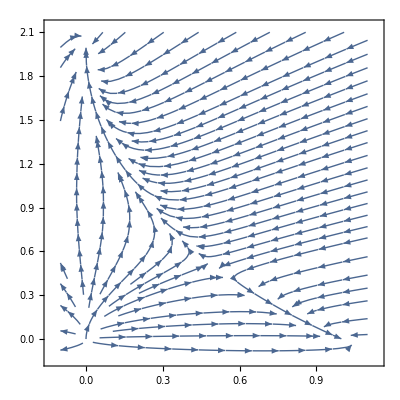

```mathematica
StreamPlot[{x-(x^2)-x*y,0.5*y-0.25*(y^2)-0.75*x*y},{x,-0.1,1.1},{y,-0.1,2.1}]
```

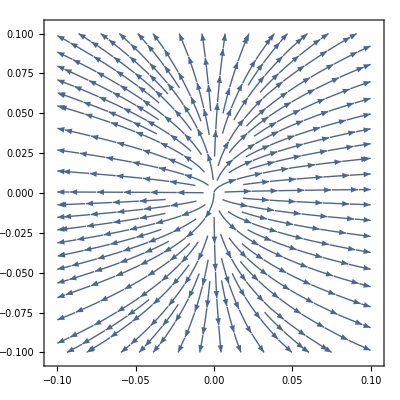

```mathematica
StreamPlot[{x-(x^2)-x*y,0.5*y-0.25*(y^2)-0.75*x*y},{x,-0.1,0.1},{y,-0.1,0.1}]
```

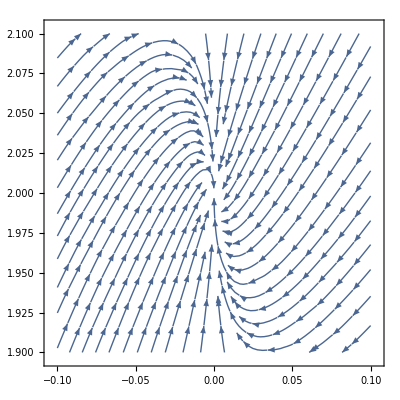

```mathematica
StreamPlot[{x-(x^2)-x*y,0.5*y-0.25*(y^2)-0.75*x*y},{x,-0.1,0.1},{y,1.9,2.1}]
```

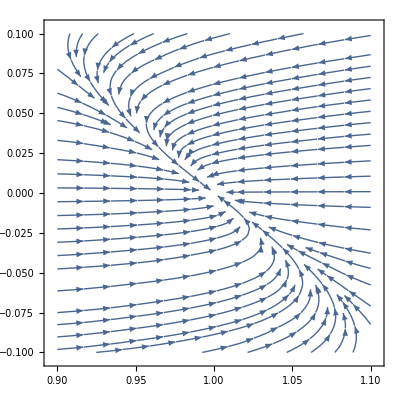

```mathematica
StreamPlot[{x-(x^2)-x*y,0.5*y-0.25*(y^2)-0.75*x*y},{x,0.9,1.1},{y,-0.1,0.1}]
```

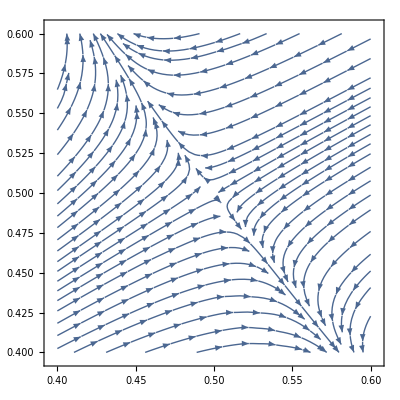

```mathematica
StreamPlot[{x-(x^2)-x*y,0.5*y-0.25*(y^2)-0.75*x*y},{x,0.4,0.6},{y,0.4,0.6}]
```